```mathematica
s=First@NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

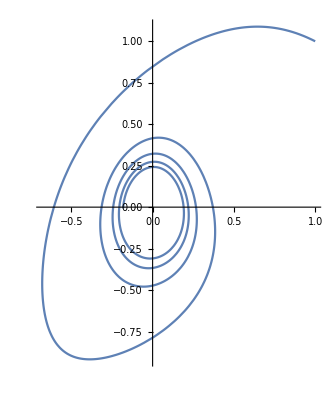

```mathematica
ParametricPlot[Evaluate[{x[k],y[k]}/.s],{k,0,20}]
```

```mathematica
Needs["MaTeX`"]
MaTeX["\\int\\frac{i x^2}{i+x^2}dx"]
κ=8 π G/c^4;
G=1;
c=1;
μ=15.614 (*[1/pc]*)
ω=μ-.1*μ;
k= μ ω
```

-Graphics-

15.614

219.417

```mathematica
j=0
```

0

```mathematica
eceins=D[Sin[θ] D[ψ[r,θ],θ],θ]+Sin[θ]D[r^2 D[ψ[r,θ],r],r]== κ Sin[θ] r^2 (μ SphericalBesselJ[j,k r] LegendreP[j,Cos[θ]])^2
```

Cos[θ] ψ^(0,1)[r,θ]+Sin[θ] ψ^(0,2)[r,θ]+Sin[θ] (2 r ψ^(1,0)[r,θ]+r^2 ψ^(2,0)[r,θ])==6127.29 r^2 Sin[θ] SphericalBesselJ[0,219.417 r]^2

```mathematica
psi=First@NDSolve[{eceins,DirichletCondition[ψ[r,θ]==-1/r,θ==π/2]},ψ,{r,0.0001,100},{θ,0,π}]
```

{ψ→InterpolatingFunction[…]}

```mathematica
Evaluate[{ψ[t,1],ψ[t,2]}/.psi]
```

{InterpolatingFunction[…][t,1],InterpolatingFunction[…][t,2]}

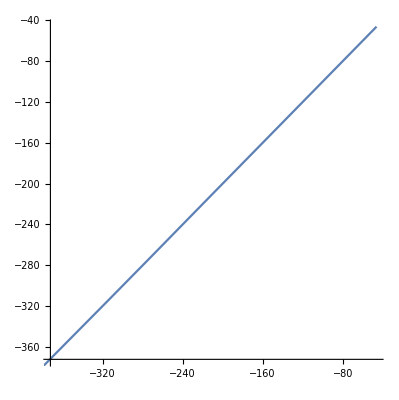

```mathematica
ParametricPlot[Evaluate[{ψ[t,1],ψ[t,2]}/.psi],{t,1,20}]
```

```mathematica
l=0.2;
```

```mathematica
s=NDSolve[{vr[t]==r'[t] ,vθ[t]==θ'[t],vθ'[t]== -(2 vr[t] vθ[t])/r[t]+(l^2 Cos[θ[t]])/(r[t]^4 Sin[θ[t]]^3), vr'[t]==r[t] vθ[t]^2 +l^2/(r[t]^3 Sin[θ[t]]^2) +u[r[t],θ[t]], vr[0]== 0,r[0]==1, vθ[0]== 1, θ[0]==π/4},{r,θ,vr,vθ},{t,0,12}]
```

NDSolve::dvnoarg: The function r appears with no arguments.

NDSolve[{vr[t]==r'[t],vθ[t]==θ'[t],vθ'[t]==(0.04 Cot[θ[t]] Csc[θ[t]]^2)/r[t]^4-(2 vr[t] vθ[t])/r[t],vr'[t]==(0.04 Csc[θ[t]]^2)/r[t]^3+r[t] vθ[t]^2+InterpolatingFunction[…][r,θ][r[t],θ[t]],vr[0]==0,r[0]==1,vθ[0]==1,θ[0]==π/4},{r,θ,vr,vθ},{t,0,12}]

```mathematica
eceins2=D[Sin[θ] ψθ[r,θ],θ]+Sin[θ]D[r^2 ψr[r,θ],r]== κ Sin[θ] r^2 (μ SphericalBesselJ[j,k r] LegendreP[j,Cos[θ]])^2
```

Cos[θ] ψθ[r,θ]+Sin[θ] ψθ^(0,1)[r,θ]+Sin[θ] (2 r ψr[r,θ]+r^2 ψr^(1,0)[r,θ])==6127.29 r^2 Sin[θ] SphericalBesselJ[0,219.417 r]^2

```mathematica
psi2=NDSolve[{eceins2,ψr[r,θ]== D[ψ[r,θ],r],ψθ[r,θ]== D[ψ[r,θ],θ],DirichletCondition[ψ[r,θ]==-1/r,θ==π/2]},{ψr,ψθ,ψ},{r,0.0001,100},{θ,0,π}]
```

NDSolve::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {ψr,ψθ}; the result may not be unique.

{{ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],ψ→InterpolatingFunction[…]}}

```mathematica
Evaluate[{ψr[t,1],ψθ[t,2]}/.psi2]
```

{{InterpolatingFunction[…][t,1],InterpolatingFunction[…][t,2]}}

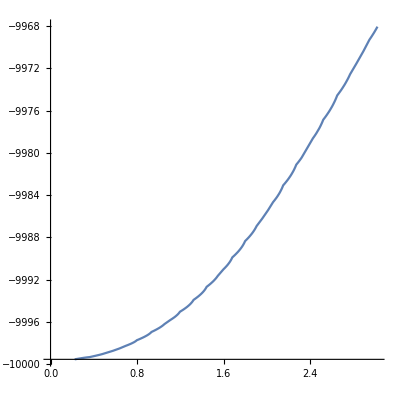

```mathematica
ParametricPlot[Evaluate[{ψr[t,1],ψ[t,1]}/.psi2],{t,1,20},AspectRatio->1]
```

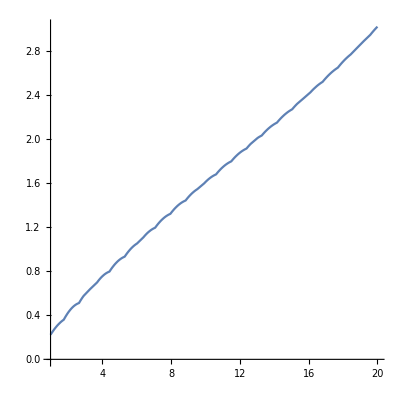

```mathematica
Plot[Evaluate[ψr[t,1]/.psi2],{t,1,20},AspectRatio->1]
```

```mathematica
Evaluate[ψr[r[t],θ[t]]/.psi2][[1]]
```

InterpolatingFunction[…][r[t],θ[t]]

```mathematica
s=NDSolve[{vr[t]==r'[t] ,vθ[t]==θ'[t],vθ'[t]== -(2 vr[t] vθ[t])/r[t]+(l^2 Cos[θ[t]])/(r[t]^4 Sin[θ[t]]^3), vr'[t]==r[t] vθ[t]^2 +l^2/(r[t]^3 Sin[θ[t]]^2) +Evaluate[ψr[r[t],θ[t]]/.psi2][[1]], vr[0]== 0,r[0]==1, vθ[0]== 1, θ[0]==π/4},{r,θ,vr,vθ},{t,3,4}]
```

NDSolve[{vr[t]==r'[t],vθ[t]==θ'[t],vθ'[t]==(l^2 Cot[θ[t]] Csc[θ[t]]^2)/r[t]^4-(2 vr[t] vθ[t])/r[t],vr'[t]==(l^2 Csc[θ[t]]^2)/r[t]^3+r[t] vθ[t]^2+ψr[r[t],θ[t]],vr[0]==0,r[0]==1,vθ[0]==1,θ[0]==π/4},{r,θ,vr,vθ},{t,3,4}]

```mathematica
.13
```